```mathematica
Clear["Global`*"];
```

Some values for fN and gN

N | a0 | fN | gN
121 | 1.5 | 0.5180
 | 0.0236
121 | 0.5 | 2.1726 | 0.1463
225 | 1.5 | 0.5185 | 0.0236
225 | 0.5 | 2.3021 | 0.1465
□ | □ | □ | □
□ | □ | □ | □
□ | □ | □ | □
□ | □ | □ | □
□ | □ | □ | □

## Fixed points of the mean-field system described by p

Solve the equation ⟨Δp⟩=0 for the well-mixed system (I=0)

```mathematica
μ[p_]:= fN*((Con-Coff)*p+Coff);
σ[p_]:=gN*(Con-Coff)^2 *p*(1-p)+ KroneckerDelta[p,0]+KroneckerDelta[p,1]; (*additional terms to suppress warning*)
Ponon[p_]:=Piecewise[{{(1-HeavisideTheta[k-(1+fN)*Con]), p==1}, {1, p==0}} , 1-CDF[NormalDistribution[μ[p],σ[p]], k-Con]];
Poffoff[p_]:= Piecewise[{{(HeavisideTheta[k-(1+fN)*Coff]), p==0}, {1, p==1}} , CDF[NormalDistribution[μ[p],σ[p]], k-1]  ];
Δp0 = HeavisideTheta[(1+fN)*Coff-k];
Δp1 = -HeavisideTheta[k-(1+fN)*Con];
Δp[p_]:= (1-KroneckerDelta[p,0])*(1-p)(1-Poffoff[p])-(1-KroneckerDelta[p,1])*p(1-Ponon[p])+ KroneckerDelta[p,0]*Δp0 + KroneckerDelta[p,1]*Δp1;
```

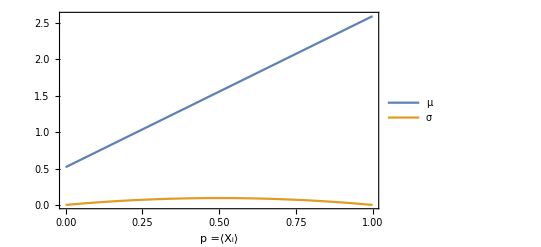

```mathematica
(* a0 = 1.5: fN-> 0.5185, gN-> 0.0236, a0=0.5: fN-> 2.3021, gN-> 0.1465*)
params = {Ncells-> 225, a0-> 1.5,fN-> 0.5185, gN-> 0.0236, Con-> 5, Coff-> 1, k-> 7.3};
Plot[{μ[p]/.params,σ[p]/.params},{p,0,1}, PlotLegends-> {"μ", "σ"}, Frame-> True, FrameLabel->{"p =⟨X_i⟩", None}]
```

Power::indet: Indeterminate expression 0.^0 encountered.

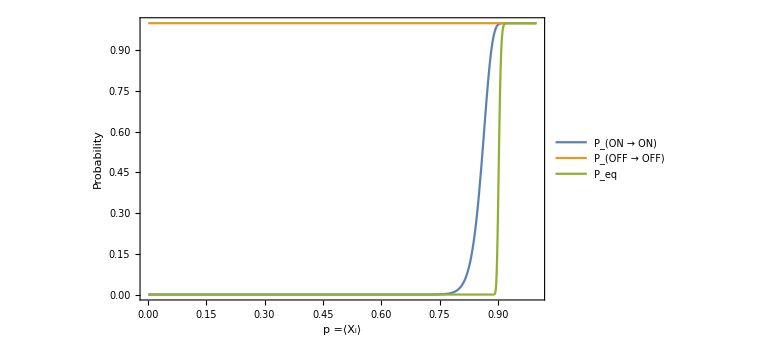

```mathematica
ϵ=0.001; (* Ponon, Poffoff not defined for p=0,1 *)
Peq[p_] :=Piecewise[{{Poffoff[p]^Ncells, p==0},{Ponon[p]^Ncells, p==1}},Ponon[p]^(Round[Ncells*p])*Poffoff[p]^(Ncells- Round[Ncells*p])];
Plot[{Ponon[p]/.params,Poffoff[p]/.params, Peq[p] /. params},{p,0+ϵ,1-ϵ}, BaseStyle->{FontSize-> 20}, ImageSize->Large, PlotLegends-> {"P_(ON →  ON)", "P_(OFF →  OFF)", "P_eq"}, Frame-> True, FrameLabel->{"p =⟨X_i⟩", "Probability"}, PlotRange-> {{0,1},{0,1}},FrameTicks->{{Automatic, None},{Automatic, None}}]
```

```mathematica
Pononvals= Table[Ponon[p]/.params, {p,0,1,1/Ncells/.params}];
Poffoffvals= Table[Poffoff[p]/.params, {p,0,1,1/Ncells/.params}];
Peqvals= Table[Peq[p]/.params, {p,0,1,1/Ncells/.params}];
pvals = Range[0,1, 1/Ncells/.params];
p1=ListPlot[Transpose[{pvals, Pononvals}],  PlotLegends-> {"P_(ON →  ON)"},PlotStyle-> ColorData[97,"ColorList"][[1]]];
p2=ListPlot[Transpose[{pvals, Poffoffvals}], PlotLegends-> {"P_(OFF →  OFF)"},PlotStyle-> ColorData[97,"ColorList"][[2]]];
p3=ListPlot[Transpose[{pvals, Peqvals}],PlotLegends-> {"P_eq"}, PlotStyle-> ColorData[97,"ColorList"][[3]]];
```

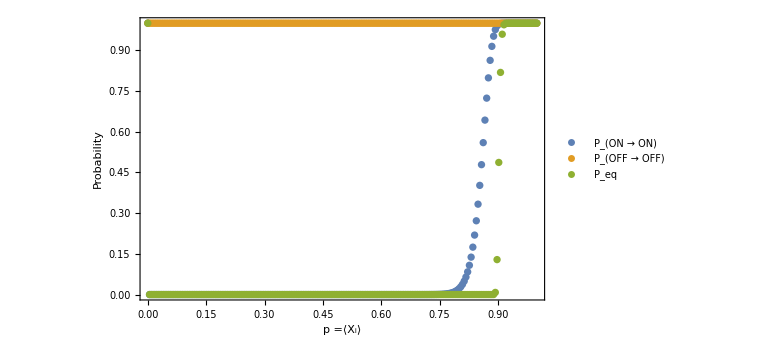

```mathematica
Show[p1,p2,p3, PlotRange-> {{0,1},{0,1}},BaseStyle->{FontSize-> 20}, ImageSize->Large,  Frame-> True, FrameLabel->{"p =⟨X_i⟩", "Probability"}, PlotRange-> {{0,1},{0,1}},FrameTicks->{{Automatic, None},{Automatic, None}}]
```

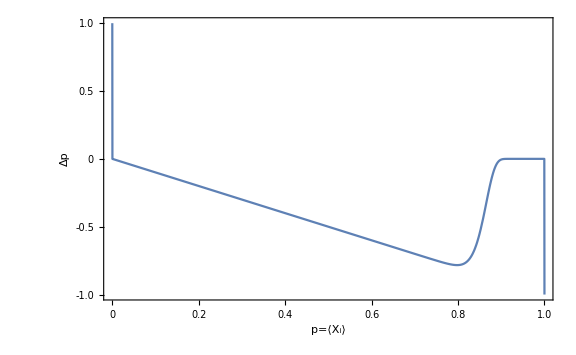

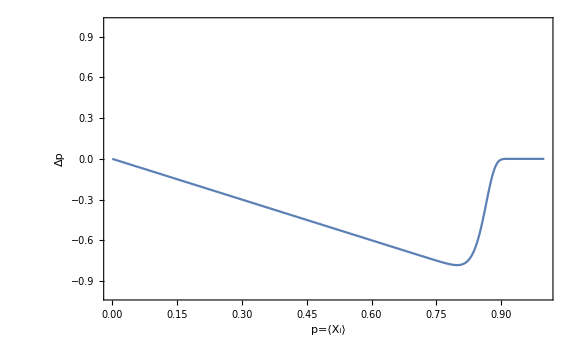

```mathematica
Plot[{Δp[p] /.params},{p,0-ϵ,1+ϵ}, Frame-> True, FrameLabel->{"p=⟨X_i⟩", "Δp"}, PlotRange-> {{0,1},{-1,1}}, FrameTicks->All]
dp=0.001;
Δpvals=Table[Δp[p] /.params,{p,0,1,dp}];
ListPlot[Transpose[{Range[0,1,dp],Δpvals}],BaseStyle->{FontSize-> 20}, ImageSize->Large, Frame-> True, FrameLabel->{"p=⟨X_i⟩", "Δp"},PlotRange-> {{0,1},{-1, 1}}, Joined-> True]
```

```mathematica
params
```

{Ncells→225,a0→1.5,fN→0.5185,gN→0.0236,Con→5,Coff→1,k→7.3}

### Solve numerically across parameter range

## Fixed points of the mean - field system described by (p, Θ)

### Generate Δp maps

```mathematica
MoranI[p_,Θ_]:=Piecewise[{{0, p==0},{0, p==1}},(Θ-fN*(2p-1)^2)/(4p(1-p)*fN)];
Θ[p_,mI_]:= fN*4p(1-p)*mI+fN*(2p-1)^2;
μOFF[p_,mI_]:= fN*(Coff+ (Con-Coff)p-(Con-1)*p*mI);
μON[p_,mI_]:= fN*(Coff+ (Con-Coff)p+(Con-1)*(1-p)*mI);
σ[p_]:=gN*(Con-Coff)^2 *p*(1-p); 
Ponon[p_,mI_]:=Piecewise[{{(1+Δp1), p==1}, {1, p==0}} , 1-CDF[NormalDistribution[μON[p,mI],σ[p]], k-Con]];
Poffoff[p_,mI_]:= Piecewise[{{(1-Δp0), p==0}, {1, p==1}} , CDF[NormalDistribution[μOFF[p,mI],σ[p]], k-1]  ];
Δp0 = HeavisideTheta[(1+fN)*Coff-k];
Δp1 = -HeavisideTheta[k-(1+fN)*Con];
Δp[p_, mI_]:= Piecewise[{{Δp0, p==0 },{Δp1, p==1}}, (1-p)(1-Poffoff[p,mI])-p(1-Ponon[p,mI])];
ΔΘ[p_, mI_]:=4*fN*Δp[p, mI]^2 - (1-KroneckerDelta[p,0])*2(Θ[p,mI]+fN(2p-1))(1-Ponon[p,mI])- (1-KroneckerDelta[p,1])*2(Θ[p,mI]-fN(2p-1))(1-Poffoff[p,mI]);
```

Some values for fN and gN

N | a0 | fN | gN
121 | 1.5 | 0.5180
 | 0.0236
121 | 0.5 | 2.1726 | 0.1463
225 | 1.5 | 0.5185 | 0.0236
225 | 0.5 | 2.3021 | 0.1465
□ | □ | □ | □
□ | □ | □ | □
□ | □ | □ | □
□ | □ | □ | □
□ | □ | □ | □

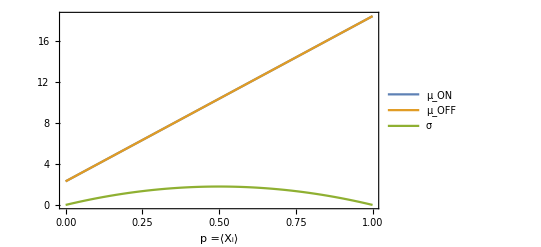

```mathematica
params = {fN-> 2.3021, gN-> 0.1465, Con-> 8, Coff-> 1, k-> 16};
Plot[{μON[p,0]/.params,μOFF[p,0]/.params, σ[p]/.params},{p,0,1}, PlotLegends-> {"μ_ON","μ_OFF", "σ"}, Frame-> True, FrameLabel->{"p =⟨X_i⟩", None}]
```

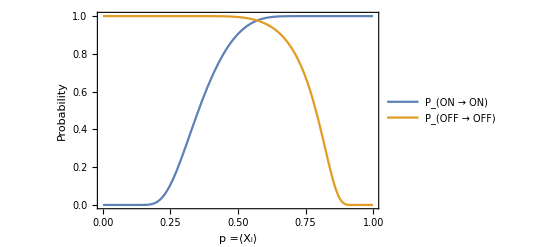

```mathematica
ϵ=0.001;
Plot[{Ponon[p, 0]/.params,Poffoff[p, 0]/.params},{p,0+ϵ,1-ϵ}, PlotLegends-> {"P_(ON →  ON)", "P_(OFF →  OFF)"}, Frame-> True, FrameLabel->{"p =⟨X_i⟩", "Probability"}, PlotRange-> {{0,1},{0,1}}]
```

```mathematica
DensityPlot[Ponon[p,mI]/. params, {p,0,1}, {mI,-0.2,0.5}, PlotLegends->Automatic, Mesh-> All];
```

Plot Δp at different values of Θ

```mathematica
Ivals = {0, 0.1, 0.2, 0.5};
legend = StringJoin["I = ", ToString[#]] & /@ Ivals;
```

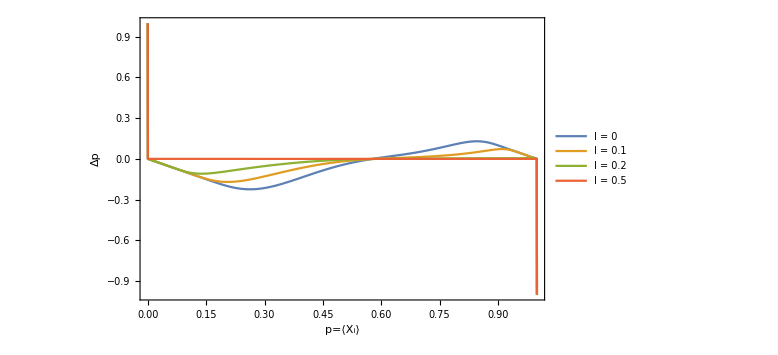

```mathematica
Plot[{Δp[p, Ivals[[1]]] /.params, Δp[p, Ivals[[2]]] /.params, Δp[p, Ivals[[3]]] /.params, Δp[p, Ivals[[4]]] /.params},{p,0-ϵ,1+ϵ}, BaseStyle->{FontSize-> 20}, PlotLegends->legend, Frame-> True, FrameLabel->{"p=⟨X_i⟩", "Δp"}, PlotRange-> {{0,1},{-1,1}}, FrameTicks->{{Automatic, None}, {Automatic, None}}, ImageSize-> Large]
```

```mathematica
params
```

{fN→2.3021,gN→0.1465,Con→8,Coff→1,k→16}

### Plot (Δp, ΔΘ) as heat map

```mathematica
dp = 0.01; dI=0.01;
Δpvals = Table[{p,mI, Δp[p,mI]/. params}, {p,0,1,dp}, {mI, -0.2,0.5,dI}];
ΔΘvals = Table[{p,mI, ΔΘ[p,mI]/. params}, {p,0,1,dp}, {mI, -0.2,0.5,dI}];
```

$Aborted

```mathematica
legend = BarLegend["TemperatureMap",{-1,1}];
ListDensityPlot[Δpvals,Mesh->True,InterpolationOrder->0, ColorFunction-> "TemperatureMap", PlotLegends-> Automatic, FrameLabel-> {"p", "I"}]
```

```mathematica
legend=  BarLegend[{"TemperatureMap",{-fN/.params,fN/.params}}];
ListDensityPlot[ΔΘvals,Mesh->None,InterpolationOrder->0, ColorFunction-> "TemperatureMap", PlotLegends-> Automatic, FrameLabel-> {"p", "I"}]
```

## Calculations

```mathematica
Δ2 =(-(ΔΘ/fN)p+(Θ/fN)Δp+Δp)/(p+Δp)(1-Ponon) -((ΔΘ/fN)(1-p)+(Θ/fN)Δp-Δp)/(1-p-Δp)(1-Poffoff);
Δ2b =(-(ΔΘ/fN)p+(Θ/fN)Δp+Δp)/(p)(1-Ponon) -((ΔΘ/fN)(1-p)+(Θ/fN)Δp-Δp)/(1-p)(1-Poffoff);
Δ2c =Piecewise[{{0, p==0}},(-(ΔΘ/fN)p+(Θ/fN)Δp+Δp)/(p+Δp)(1-Ponon)] -Piecewise[{{0, p==1}},((ΔΘ/fN)(1-p)+(Θ/fN)Δp-Δp)/(1-p-Δp)(1-Poffoff)];
Δ2d =(1-KroneckerDelta[p,0])*(-(ΔΘ/fN)p+(Θ/fN)Δp+Δp)/(p+Δp)(1-Ponon)-(1-KroneckerDelta[p,1])((ΔΘ/fN)(1-p)+(Θ/fN)Δp-Δp)/(1-p-Δp)(1-Poffoff);
Δ1 = -2(Θ+ fN(2p-1))(1-Ponon) - 2(Θ-fN(2p-1))(1-Poffoff);
Δ1b = (1-KroneckerDelta[p,0]) -2(Θ+ fN(2p-1))(1-Ponon) -(1-KroneckerDelta[p,1])2(Θ-fN(2p-1))(1-Poffoff);sol=Solve[ΔΘ == Δ1b+ Δ2d, ΔΘ]
```

{{ΔΘ→(1-2 (1-Ponon) (fN (-1+2 p)+Θ)+((1-Ponon) Δp (1-0,p))/(p+Δp)+((1-Ponon) Δp Θ (1-0,p))/(fN (p+Δp))-0,p+((1-Poffoff) Δp (1-1,p))/(1-p-Δp)-((1-Poffoff) Δp Θ (1-1,p))/(fN (1-p-Δp))-2 (1-Poffoff) (-fN (-1+2 p)+Θ) (1-1,p))/(1+(p (1-Ponon) (1-0,p))/(fN (p+Δp))+((1-p) (1-Poffoff) (1-1,p))/(fN (1-p-Δp)))}}

```mathematica
sol//Expand//FullSimplify
```

{{ΔΘ→(-2 fN^2 (-1+2 p) (Poffoff-Ponon) (-1+p+Δp) (p+Δp)-Δp (1-Ponon+p (-2+Poffoff+Ponon)+(-2+Poffoff+Ponon) Δp) Θ+fN (-p+p^2-2 Δp+2 p Δp+p Poffoff Δp+Ponon Δp-p Ponon Δp+Δp^2+Poffoff Δp^2-Ponon Δp^2+2 (-2+Poffoff+Ponon) (-1+p+Δp) (p+Δp) Θ)-(-1+p+Δp) (fN (p+2 Δp-Ponon Δp)-(-1+Ponon) Δp Θ) 0,p+(-1+Poffoff) (p+Δp) (-fN Δp+2 fN^2 (-1+2 p) (-1+p+Δp)+Δp Θ-2 fN (-1+p+Δp) Θ) 1,p)/((-1+p) p (2+fN-Poffoff-Ponon)+(-1+fN (-1+2 p)+Poffoff-p (-2+Poffoff+Ponon)) Δp+fN Δp^2+p (-1+Ponon) (-1+p+Δp) 0,p+(-1+p) (-1+Poffoff) (p+Δp) 1,p)}}